## 英語

```mathematica
f=Exp[-Log[x/(1.6)]^2]
```

ⅇ^(-Log[0.625 x]^2)

```mathematica
mv=MaxValue[f,x]
```

1.

```mathematica
am=ArgMax[f,x]
```

1.6

```mathematica
last=10
```

10

```mathematica
peakPoint={am,mv}
peakPointBotom={am,0}
peakZero={0,mv}
```

{1.6,1.}

{1.6,0}

{0,1.}

```mathematica
x["d"]=8
c["d"]=f/.x->x["d"]//N
x["d-1"]=7.5
c["d-1"]=f/.x->x["d-1"]//N
```

8

0.0749983

7.5

0.0919313

```mathematica
arrowY=0.066
arrow1=Arrow[{{0,arrowY},{am,arrowY}}]
arrow2=Arrow[{{am,arrowY},{x["d"],arrowY}}]
arrow3=Arrow[{{x["d"],arrowY},{last,arrowY}}]
```

0.066

Arrow[{{0,0.066},{1.6,0.066}}]

Arrow[{{1.6,0.066},{8,0.066}}]

Arrow[{{8,0.066},{10,0.066}}]

```mathematica
textAx=Text[Style["Number of cited per year",12],{0.2,1.13}]
textF=Text[Style["C(x)",17],{1.5,1.04}]
textPk=Text["Peak count",{-0.45,1}]
textPY=Text["Publish year",{-0.5,-0.09}]
textFC=Text["First cited\nyear",{0.5,-0.09}]
textPkY=Text["Peak year",{1.8,-0.09}]
textDY=Text["Decay year",{8.5,-0.09}]
textLY=Text["Last year",{10.5,-0.09}]
textPd1=Text["Peak period",{0.9,0.1}]
textPd2=Text["Decay period",{4,0.1}]
textPd3=Text["Sustain period",{9,0.1}]
textX0=Text[Style["0",17],{-0.05,-0.01}]
textXc=Text[Style["x_c",17],{0.4,-0.01}]
textXp=Text[Style["x_p",17],{1.6,-0.01}]
textXd1=Text[Style["x_(d - 1)",17],{7.4,-0.01}]
textXd=Text[Style["x_d",17],{8,-0.01}]
textXl=Text[Style["x_l",17],{10,-0.01}]
textAA=Text[Style["A",Bold,17],{2,0.4}]
textAB=Text[Style["B",Bold,17],{7.75,0.025}]
textAC=Text[Style["C",Bold,17],{9,0.024}]
textY=Text[Style["Elapsed year",12],{10.8,0.01}]
```

Text[Number of cited per year,{0.2,1.13}]

Text[C(x),{1.5,1.04}]

Text[Peak count,{-0.45,1}]

Text[Publish year,{-0.5,-0.09}]

Text[First cited
year,{0.5,-0.09}]

Text[Peak year,{1.8,-0.09}]

Text[Decay year,{8.5,-0.09}]

Text[Last year,{10.5,-0.09}]

Text[Peak period,{0.9,0.1}]

Text[Decay period,{4,0.1}]

Text[Sustain period,{9,0.1}]

Text[0,{-0.05,-0.01}]

Text[x_c,{0.4,-0.01}]

Text[x_p,{1.6,-0.01}]

Text[x_(d - 1),{7.4,-0.01}]

Text[x_d,{8,-0.01}]

Text[x_l,{10,-0.01}]

Text[A,{2,0.4}]

Text[B,{7.75,0.025}]

Text[C,{9,0.024}]

Text[Elapsed year,{10.8,0.01}]

```mathematica
textDef=Text["Definition: ",{9,1.05},Left]
def1=Text["Area A: ∫_0^(x_(d - 1)) C(x)ⅆx",{9,0.95},Left]
def2=Text["Area B: ∫_(x_(d - 1))^x_d C(x)ⅆx",{9,0.85},Left]
def3=Text["Area C: ∫_x_d^x_l C(x)ⅆx",{9,0.75},Left]
def4=Text["x_d: min(x)|B/(A + B)≤0.05",{9,0.65},Left]
def5=Text["Total cited: A+B+C",{9,0.55},Left]
con1=Text["Condition:",{5,1.05},Left]
con2=Text["・Peak period + Decay period ≥ 10",{5,0.98},Left]
con3=Text["・Peak period ≤ Decay period",{5,0.91},Left]
con4=Text["(:30fbx)_d exists",{5,0.84},Left]
```

Text[Definition: ,{9,1.05},Left]

Text[Area A: ∫_0^(x_(d - 1)) C(x)ⅆx,{9,0.95},Left]

Text[Area B: ∫_(x_(d - 1))^x_d C(x)ⅆx,{9,0.85},Left]

Text[Area C: ∫_x_d^x_l C(x)ⅆx,{9,0.75},Left]

Text[x_d: min(x)|B/(A + B)≤0.05,{9,0.65},Left]

Text[Total cited: A+B+C,{9,0.55},Left]

Text[Condition:,{5,1.05},Left]

Text[・Peak period + Decay period ≥ 10,{5,0.98},Left]

Text[・Peak period ≤ Decay period,{5,0.91},Left]

Text[(・x)_d exists,{5,0.84},Left]

{Line[{{7.5,0},{7.5,0.0919313}}],Line[{{8,0},{8,0.0749983}}],Line[{{10,0},{10,0.1}}],Arrowheads[{-0.025,0.025}],Arrow[{{0,0.066},{1.6,0.066}}],Arrow[{{1.6,0.066},{8,0.066}}],Arrow[{{8,0.066},{10,0.066}}],Dashing[{Small,Small}],Line[{{1.6,1.},{1.6,0}}],Line[{{1.6,1.},{0,1.}}],Text[Number of cited per year,{0.2,1.13}],Text[C(x),{1.5,1.04}],Text[Peak count,{-0.45,1}],Text[Publish year,{-0.5,-0.09}],Text[First cited
year,{0.5,-0.09}],Text[Peak year,{1.8,-0.09}],Text[Decay year,{8.5,-0.09}],Text[Last year,{10.5,-0.09}],Text[Peak period,{0.9,0.1}],Text[Decay period,{4,0.1}],Text[Sustain period,{9,0.1}],Text[0,{-0.05,-0.01}],Text[x_c,{0.4,-0.01}],Text[x_p,{1.6,-0.01}],Text[x_(d - 1),{7.4,-0.01}],Text[x_d,{8,-0.01}],Text[x_l,{10,-0.01}],Text[A,{2,0.4}],Text[B,{7.75,0.025}],Text[C,{9,0.024}],Text[Elapsed year,{10.8,0.01}],Text[Definition: ,{9,1.05},Left],Text[Area A: ∫_0^(x_(d - 1)) C(x)ⅆx,{9,0.95},Left],Text[Area B: ∫_(x_(d - 1))^x_d C(x)ⅆx,{9,0.85},Left],Text[Area C: ∫_x_d^x_l C(x)ⅆx,{9,0.75},Left],Text[x_d: min(x)|B/(A + B)≤0.05,{9,0.65},Left],Text[Total cited: A+B+C,{9,0.55},Left],Text[Condition:,{5,1.05},Left],Text[・Peak period + Decay period ≥ 10,{5,0.98},Left],Text[・Peak period ≤ Decay period,{5,0.91},Left],Text[(・x)_d exists,{5,0.84},Left]}

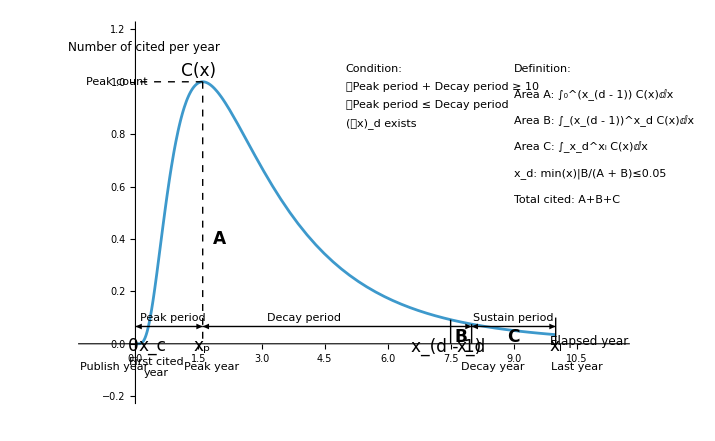

```mathematica
epob={Line[{{x["d-1"],0},{x["d-1"],c["d-1"]}}],Line[{{x["d"],0},{x["d"],c["d"]}}],Line[{{last,0},{last,0.1}}],Arrowheads[{-0.025,0.025}],arrow1,arrow2,arrow3,Dashed,Line[{peakPoint,peakPointBotom}],Line[{peakPoint,peakZero}],textAx,textF,textPk,textPY,textFC,textPkY,textDY,textLY,textPd1,textPd2,textPd3,textX0,textXc,textXp,textXd1,textXd,textXl,textAA,textAB,textAC,textY,textDef,def1,def2,def3,def4,def5,con1,con2,con3,con4}
Plot[f,{x,0,last},Ticks->None,Epilog->epob,PlotRange->{{-1.1,last+1.5},{-0.2,1.2}}]
```

## 日本語

```mathematica
jtextAx=Text[Style["被引用数（年間）",12],{0.2,1.13}]
jtextF=Text[Style["C(x)",17],{1.5,1.04}]
jtextPk=Text["最大被引用数",{-0.45,1}]
jtextPY=Text["出版後年数",{-0.5,-0.09}]
jtextFC=Text["第一回\n被引用年",{0.5,-0.09}]
jtextPkY=Text["最大被引用年",{1.8,-0.09}]
jtextDY=Text["減衰年",{8.2,-0.09}]
jtextLY=Text["最終年",{10.2,-0.09}]
jtextPd1=Text["最大被引用までの期間",{0.9,0.1}]
jtextPd2=Text["減衰期間",{4,0.1}]
jtextPd3=Text["減衰後の期間",{9,0.1}]
jtextX0=Text[Style["0",17],{-0.05,-0.01}]
jtextXc=Text[Style["x_c",17],{0.4,-0.01}]
jtextXp=Text[Style["x_p",17],{1.6,-0.01}]
jtextXd1=Text[Style["x_(d - 1)",17],{7.4,-0.01}]
jtextXd=Text[Style["x_d",17],{8,-0.01}]
jtextXl=Text[Style["x_l",17],{10,-0.01}]
jtextAA=Text[Style["A",Bold,17],{2,0.4}]
jtextAB=Text[Style["B",Bold,17],{7.75,0.025}]
jtextAC=Text[Style["C",Bold,17],{9,0.024}]
jtextY=Text[Style["出版からの年数",12],{10.8,0.01}]
```

Text[被引用数（年間）,{0.2,1.13}]

Text[C(x),{1.5,1.04}]

Text[最大被引用数,{-0.45,1}]

Text[出版後年数,{-0.5,-0.09}]

Text[第一回
被引用年,{0.5,-0.09}]

Text[最大被引用年,{1.8,-0.09}]

Text[減衰年,{8.2,-0.09}]

Text[最終年,{10.2,-0.09}]

Text[最大被引用までの期間,{0.9,0.1}]

Text[減衰期間,{4,0.1}]

Text[減衰後の期間,{9,0.1}]

Text[0,{-0.05,-0.01}]

Text[x_c,{0.4,-0.01}]

Text[x_p,{1.6,-0.01}]

Text[x_(d - 1),{7.4,-0.01}]

Text[x_d,{8,-0.01}]

Text[x_l,{10,-0.01}]

Text[A,{2,0.4}]

Text[B,{7.75,0.025}]

Text[C,{9,0.024}]

Text[出版からの年数,{10.8,0.01}]

```mathematica
jtextDef=Text["定義: ",{9,1.05},Left]
jdef1=Text["A: ∫_0^(x_(d - 1)) C(x)ⅆx",{9,0.95},Left]
jdef2=Text["B: ∫_(x_(d - 1))^x_d C(x)ⅆx",{9,0.85},Left]
jdef3=Text["C: ∫_x_d^x_l C(x)ⅆx",{9,0.75},Left]
jdef4=Text["x_d: min(x)|B/(A + B)≤0.05",{9,0.65},Left]
jdef5=Text["被引用総数: A+B+C",{9,0.55},Left]
jcon1=Text["オブソレッセンス到達の条件:",{5,1.05},Left]
jcon2=Text["・最大被引用までの期間 + 減衰期間 ≥ 10年",{5,0.98},Left]
jcon3=Text["・最大被引用までの期間 ≤ 減衰期間",{5,0.91},Left]
jcon4=Text["(:30fbx)_d が存在する",{5,0.84},Left]
```

Text[定義: ,{9,1.05},Left]

Text[A: ∫_0^(x_(d - 1)) C(x)ⅆx,{9,0.95},Left]

Text[B: ∫_(x_(d - 1))^x_d C(x)ⅆx,{9,0.85},Left]

Text[C: ∫_x_d^x_l C(x)ⅆx,{9,0.75},Left]

Text[x_d: min(x)|B/(A + B)≤0.05,{9,0.65},Left]

Text[被引用総数: A+B+C,{9,0.55},Left]

Text[オブソレッセンス到達の条件:,{5,1.05},Left]

Text[・最大被引用までの期間 + 減衰期間 ≥ 10年,{5,0.98},Left]

Text[・最大被引用までの期間 ≤ 減衰期間,{5,0.91},Left]

Text[(・x)_d が存在する,{5,0.84},Left]

{Line[{{7.5,0},{7.5,0.0919313}}],Line[{{8,0},{8,0.0749983}}],Line[{{10,0},{10,0.1}}],Arrowheads[{-0.025,0.025}],Arrow[{{0,0.066},{1.6,0.066}}],Arrow[{{1.6,0.066},{8,0.066}}],Arrow[{{8,0.066},{10,0.066}}],Dashing[{Small,Small}],Line[{{1.6,1.},{1.6,0}}],Line[{{1.6,1.},{0,1.}}],Text[被引用数（年間）,{0.2,1.13}],Text[C(x),{1.5,1.04}],Text[最大被引用数,{-0.45,1}],Text[第一回
被引用年,{0.5,-0.09}],Text[最大被引用年,{1.8,-0.09}],Text[減衰年,{8.2,-0.09}],Text[最終年,{10.2,-0.09}],Text[最大被引用までの期間,{0.9,0.1}],Text[減衰期間,{4,0.1}],Text[減衰後の期間,{9,0.1}],Text[0,{-0.05,-0.01}],Text[x_c,{0.4,-0.01}],Text[x_p,{1.6,-0.01}],Text[x_(d - 1),{7.4,-0.01}],Text[x_d,{8,-0.01}],Text[x_l,{10,-0.01}],Text[A,{2,0.4}],Text[B,{7.75,0.025}],Text[C,{9,0.024}],Text[出版からの年数,{10.8,0.01}],Text[定義: ,{9,1.05},Left],Text[A: ∫_0^(x_(d - 1)) C(x)ⅆx,{9,0.95},Left],Text[B: ∫_(x_(d - 1))^x_d C(x)ⅆx,{9,0.85},Left],Text[C: ∫_x_d^x_l C(x)ⅆx,{9,0.75},Left],Text[x_d: min(x)|B/(A + B)≤0.05,{9,0.65},Left],Text[被引用総数: A+B+C,{9,0.55},Left],Text[オブソレッセンス到達の条件:,{5,1.05},Left],Text[・最大被引用までの期間 + 減衰期間 ≥ 10年,{5,0.98},Left],Text[・最大被引用までの期間 ≤ 減衰期間,{5,0.91},Left],Text[(・x)_d が存在する,{5,0.84},Left]}

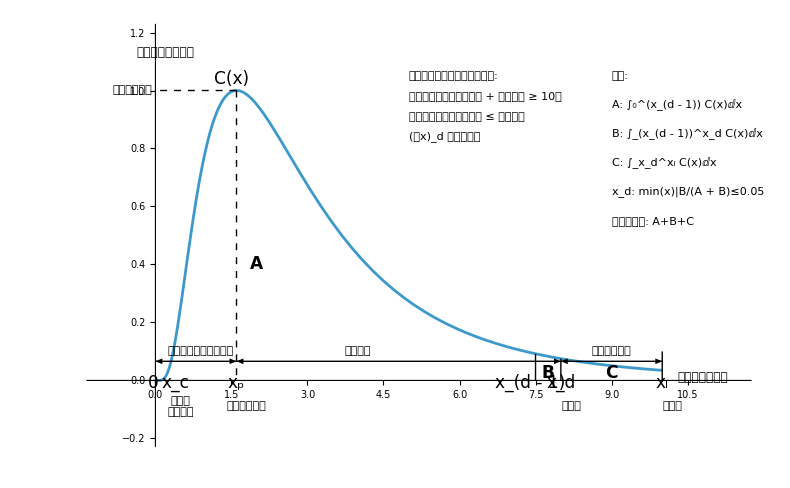

```mathematica
epob={Line[{{x["d-1"],0},{x["d-1"],c["d-1"]}}],Line[{{x["d"],0},{x["d"],c["d"]}}],Line[{{last,0},{last,0.1}}],Arrowheads[{-0.025,0.025}],arrow1,arrow2,arrow3,Dashed,Line[{peakPoint,peakPointBotom}],Line[{peakPoint,peakZero}],jtextAx,jtextF,jtextPk,jtextFC,jtextPkY,jtextDY,jtextLY,jtextPd1,jtextPd2,jtextPd3,jtextX0,jtextXc,jtextXp,jtextXd1,jtextXd,jtextXl,jtextAA,jtextAB,jtextAC,jtextY,jtextDef,jdef1,jdef2,jdef3,jdef4,jdef5,jcon1,jcon2,jcon3,jcon4}
Plot[f,{x,0,last},Ticks->None,Epilog->epob,PlotRange->{{-1.1,last+1.5},{-0.2,1.2}}]
```